```mathematica
SetDirectory[NotebookDirectory[]];
Needs["GLSTools`"];
```

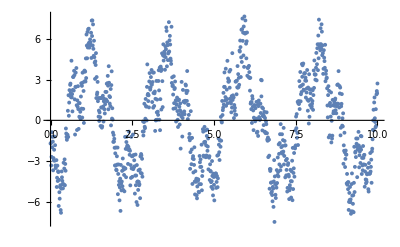

```mathematica
(* Make some fake data *)
t = Range[0.0,10.0,0.01];
y = 4Cos[2.7t + 3.0]+2 Sin[10.7t+1.0] + RandomVariate[NormalDistribution[],Length@t];
ivar = ConstantArray[1, Length@t];
ListPlot[Transpose[{t,y}]]
```

```mathematica
fund = 2Pi/10.0;
freqs = Range[fund, 100,fund];
Length@freqs
```

159

```mathematica
pp =GLS[t,y,ivar,freqs];
fap = FAP[t,y,ivar,freqs,50];
```

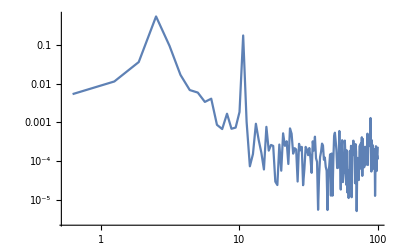

```mathematica
ListLogLogPlot[Transpose[{freqs,pp}],PlotRange->Full,Joined->True]
```

```mathematica
Quantile[fap,0.99]
```

0.00901041